```mathematica
eqns = {L*i'[t] == vq-i[t]*R-Kt*Sqrt[3/2]*w[t],J*w'[t] == Kt*Sqrt[3/2]*i[t]-Bv*w[t]-Tl, i[0]==0, w[0]==0}
```

{L i'[t]==vq-R i[t]-√(3/2) Kt w[t],J w'[t]==-Tl+√(3/2) Kt i[t]-Bv w[t],i[0]==0,w[0]==0}

```mathematica
params = {L->1.17*^-4, J->6.5*^-6, Kt->0.00255, R->0.117, Bv->2.415*^-6}
```

{L→0.000117,J→6.5×10^-6,Kt→0.00255,R→0.117,Bv→2.415×10^-6}

```mathematica
xsol = DSolve[eqns, {i,w},t]//Simplify;
```

```mathematica
$eqns[$vq_,$Tl_] = eqns/.params/.{vq->$vq, Tl->$Tl}
```

{0.000117 i'[t]==$vq-0.117 i[t]-0.0031231 w[t],6.5×10^-6 w'[t]==-$Tl+0.0031231 i[t]-2.415×10^-6 w[t],i[0]==0,w[0]==0}

```mathematica
$eqns[1,0]
```

{0.000117 i'[t]==1-0.117 i[t]-0.0031231 w[t],6.5×10^-6 w'[t]==0.0031231 i[t]-2.415×10^-6 w[t],i[0]==0,w[0]==0}

```mathematica
sol=First@NDSolve[$eqns[Sqrt[3/2]*1,0], {i,w},{t,0,10}, MaxStepSize->0.0001]
```

{i→InterpolatingFunction[{{0., 10.}}, <>],w→InterpolatingFunction[{{0., 10.}}, <>]}

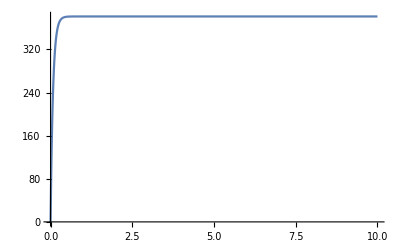

```mathematica
Plot[w[t]/.sol,{t,0,10}, PlotRange->Full]
```